# Optical resonator mode matching

P. Huft

## Gaussian beam params, matrices, functions

```mathematica
MProp[d_]:={{1,d},{0,1}};
MRefract[n1_,n2_,r_]:={{1,0},{(n1-n2)/(n2 r),n1/n2}};
MLens [f_]:= {{1,0},{-1/f,1}};
qM[q_,M_]:= (q M[[1,1]]+M[[1,2]])/(q M[[2,1]]+M[[2,2]]);
wq[q_,z_]:=√(λ/(π Im[1/(q+z)]));
w[z_,w0_]:= w0(1+((z λ)/(π w0^2))^2)^(1/2);
beamPropagate[qInit_,sys_]:=Module[{q=qInit,qNext,plots={},i,element,z=0,zNext,x},
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[plots,Piecewise[{{wq[qNext,x-z]/10^-3,z<x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
]; (*waist in [m]*)
Plot[plots,{x,0,z},PlotRange->{0,All},Frame->False]
](*q after transformation M*)
```

```mathematica
MRefract[]
```

MRefract[]

## Solve for mode-matching lenses and/or lens placement

### Rough estimate

```mathematica
R = 0.005;
f=-R/2;
λ=7.8*^-7;
x=w[R,5*^-6];(*waist at cavity mirror if given waist at focus*)
"waist at thin mirror [mm]"
x*10^3
θ=x/R;(*angle the beam exits the mirror*)
"virtual focus behind thin mirror [mm]"
x/Tan[-1/f x+θ] 10^3(*distance to virtual focus from which the beam exiting the mirror comes*)
```

waist at thin mirror [mm]

0.248332

virtual focus behind thin mirror [mm]

1.65431

```mathematica
θ
```

0.0496664

```mathematica
x
```

0.000248332

```mathematica
Sin[θ]
```

0.049646

### Gaussian solver

Cavity and beam params, and compound transformations. All distances in [m]

```mathematica
w0 = 0.0005; (*starting waist, measured*)
λ=7.8*^-7;
ng =1.45;(*index of ref. fused silica*)
mt = 6.35*^-3;(*mirror thickness*)
wt =0.005;(*can window thickness*)
gap = 0.03; (*approx distance between window and first cav mirror*)
R = 0.1; (*mirror RoC*)
LCav=0.085; (*cavity length*)
MMirror1 = MRefract[ng,1,R].MProp[mt]. MRefract[1,ng,∞]; (*input mirror*)
MMirror2 = MRefract[ng,1,∞].MProp[mt]. MRefract[1,ng,-R]; (*output mirror*)
MWindow = MRefract[ng,1,∞].MProp[wt]. MRefract[1,ng,∞]; (*flat window*)
q0 = -ⅈ (π w0^2)/λ; (*initial beam parameter*)
wCav = √((λ R)/(2 π));(*approx TEM00 waist to match in cavity*)
qCav = (-ⅈ π)/λ wCav^2;(*q param for beam at cavity waist location*)

zR = (π wCav^2)/λ; (*cavity mode Rayleigh range*)
√(λ/(π Im[1/(qCav +zR)]))/wCav ==√2(*Rayleigh range waist as sanity check*)
```

True

Beam waist and RoC immediately after the first cavity mirror

```mathematica
qIn = qCav - LCav/2; 
"roc after input mirror"
rocIn = 1/Re[1/qIn]
"waist after input mirror"
wIn = √(λ/(π Im[1/(qIn)]))
```

roc after input mirror

-0.101324

waist after input mirror

0.00014623

Set two params, solve for other two. The initial beam is transformed by lens f1, propagates d1, transformed by f2, then propagates d2 to first cavity mirror.

```mathematica
Clear[d1,f1,d2,f2]
d2= .10;
d1= .05;
freeVars ={f1,f2};
zWaist = LCav/2; (*axial waist location, measured from first cav mirror*)
MToCav = MMirror1.MProp[d2].MLens[f2].MProp[d1].MLens[f1];
roc1= FullSimplify[Chop[Refine[ComplexExpand[1/Re[1/qM[q0,MToCav]],freeVars∈Reals]]]] ; (*RoC after first cav mirror*)
wMidCav= FullSimplify[Chop[Refine[√(λ ComplexExpand[1/(π Im[1/qM[q0,MProp[zWaist].MToCav]])]),freeVars∈Reals]]];(*waist at desired target location*)
```

Solve the system

```mathematica
soln=NSolve[{roc1==rocIn,wMidCav==wCav},{f1,f2},Reals,WorkingPrecision->16]
```

{{f1→0.197422438772253,f2→3.66871437518742},{f1→0.264524793670504,f2→0.524098119318297},{f1→0.0286248182339208,f2→0.0186556010224018},{f1→0.027609333215255,f2→0.0195898875235561}}

Numerical check

```mathematica
idx = 1; (*soln to use*)
"RoC after input cav mirror, waist at target location:"
{1/Re[1/qM[q0,MToCav/.soln[[idx]]]],√(λ/(π Im[1/qM[q0,MToCav.MProp[LCav/2]/.soln[[idx]]]]))}
"RoC just before output cav mirror:"
1/Re[1/(qM[q0,MToCav/.soln[[idx]]]+LCav)]
```

RoC after input cav mirror, waist at target location:

{-0.101324,0.000126876}

RoC just before output cav mirror:

0.0929117

### Gaussian solver - Fabry-Perot

Cavity and beam params, and compound transformations. All distances in [m]

```mathematica
w0 = 0.0005; (*starting waist*)
λ=7.8*^-7;
ng =1.45;(*index of ref. fused silica*)
mt = 6.35*^-3;(*mirror thickness*)
R = 0.1; (*mirror RoC*)
LCav=0.085; (*cavity length*)
MMirror1 = MRefract[ng,1,R].MProp[mt]. MRefract[1,ng,∞]; (*input mirror*)
MMirror2 = MRefract[ng,1,∞].MProp[mt]. MRefract[1,ng,-R]; (*output mirror*)
q0 = -ⅈ (π w0^2)/λ; (*initial beam parameter*)
wCav = √((λ R)/(2 π));(*approx TEM00 waist to match in cavity*)
qCav = (-ⅈ π)/λ wCav^2;(*q param for beam at cavity waist location*)

zR = (π wCav^2)/λ; (*cavity mode Rayleigh range*)
√(λ/(π Im[1/(qCav +zR)]))/wCav ==√2(*Rayleigh range waist as sanity check*)
```

True

Beam waist and RoC immediately after the first cavity mirror

```mathematica
qIn = qCav - LCav/2; 
"roc after input mirror"
rocIn = 1/Re[1/qIn]
"waist after input mirror"
wIn = √(λ/(π Im[1/(qIn)]))
```

roc after input mirror

-0.101324

waist after input mirror

0.00014623

Set two params, solve for other two. The initial beam is transformed by lens f1, propagates d1, transformed by f2, then propagates d2 to first cavity mirror.

```mathematica
Clear[d1,f1,d2,f2]
d2= .10;
d1= .05;
freeVars ={f1,f2};
zWaist = LCav/2; (*axial waist location, measured from first cav mirror*)
MToCav = MMirror1.MProp[d2].MLens[f2].MProp[d1].MLens[f1];
roc1= FullSimplify[Chop[Refine[ComplexExpand[1/Re[1/qM[q0,MToCav]],freeVars∈Reals]]]] ; (*RoC after first cav mirror*)
wMidCav= FullSimplify[Chop[Refine[√(λ ComplexExpand[1/(π Im[1/qM[q0,MProp[zWaist].MToCav]])]),freeVars∈Reals]]];(*waist at desired target location*)
```

Solve the system

```mathematica
soln=NSolve[{roc1==rocIn,wMidCav==wCav},{f1,f2},Reals,WorkingPrecision->16]
```

{{f1→0.197422438772253,f2→3.66871437518741},{f1→0.264524793670504,f2→0.524098119318297},{f1→0.0286248182339153,f2→0.0186556010224069},{f1→0.0276093332152605,f2→0.019589887523551}}

Numerical check

```mathematica
idx = 1; (*soln to use*)
"RoC after input cav mirror, waist at target location:"
{1/Re[1/qM[q0,MToCav/.soln[[idx]]]],√(λ/(π Im[1/qM[q0,MToCav.MProp[LCav/2]/.soln[[idx]]]]))}
"RoC just before output cav mirror:"
1/Re[1/(qM[q0,MToCav/.soln[[idx]]]+LCav)]
```

RoC after input cav mirror, waist at target location:

{-0.101324,0.000126876}

RoC just before output cav mirror:

0.0929117

## Waist propagation plot - thin lenses

- “system” is a list of transformations, where each transformation is of the form {transform, distance to travel after transform}
- dashed lines indicate cavity boundaries, and blue curve between them is the target TEM00 mode.

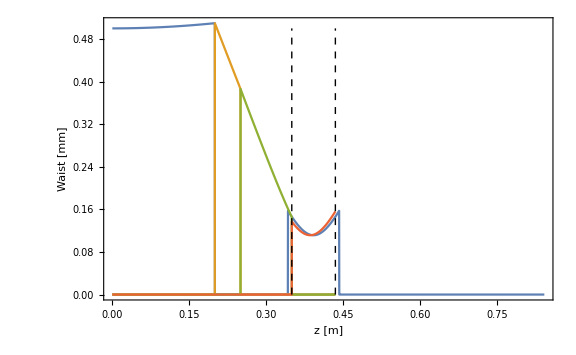

```mathematica
zR=(π wCav^2)/λ;
qStart =q0;
d0=.20; 
dCavity =d0+d1+d2+ LCav/2;
system={
{{{1,0},{0,1}},d0},
{MLens[f1],d1},
{MLens[f2],d2},
{MMirror1,LCav}
}/.soln[[1]];
Show[Plot[Piecewise[{{w[z-dCavity,wCav]/10^-3,dCavity-zR<z <dCavity+zR}}],{z,0,dCavity+zR+0.4},PlotRange->{0,1.1w0/10^-3}],beamPropagate[qStart,system],Graphics[{Dashed,Line[{{dCavity-LCav/2,0},{dCavity-LCav/2,w0/10^-3}}]}],
Graphics[{Dashed,Line[{{dCavity+LCav/2,0},{dCavity+LCav/2,w0/10^-3}}]}],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

Plot an approximate solution with lenses on hand

0.15

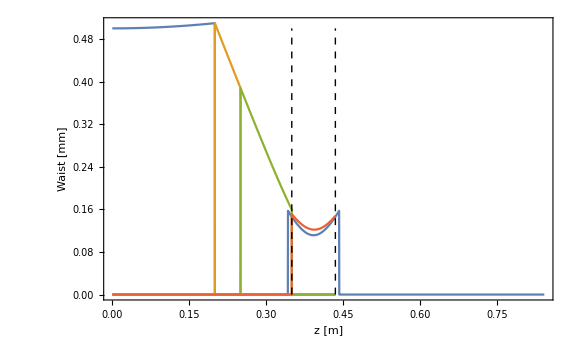

```mathematica
d0=.20; 
dCavity =d0+d1+d2+ LCav/2;
Print[d1+d2]
system={
{{{1,0},{0,1}},d0},
{MLens[f1],d1}/.f1-> .2,
{MLens[f2],d2}/.f2->∞,
{MMirror1,LCav}
}/.soln[[1]];
Show[Plot[Piecewise[{{w[z-dCavity,wCav]/10^-3,dCavity-zR<z <dCavity+zR}}],{z,0,dCavity+zR+0.4},PlotRange->{0,1.1w0/10^-3}],beamPropagate[qStart,system],Graphics[{Dashed,Line[{{dCavity-LCav/2,0},{dCavity-LCav/2,w0/10^-3}}]}],
Graphics[{Dashed,Line[{{dCavity+LCav/2,0},{dCavity+LCav/2,w0/10^-3}}]}],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

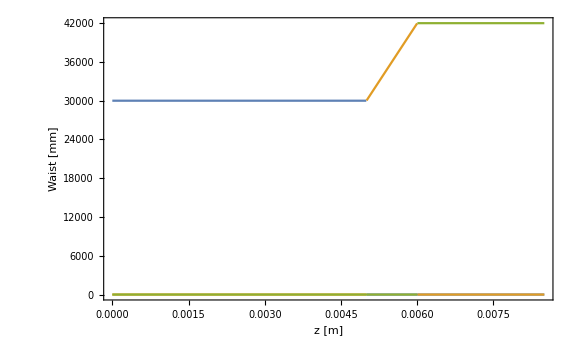

```mathematica
R = 0.005;
LCav = 2*R;
f=-R/2;
λ=7.8*^-7;
w0=5*-6; (*waist in μm*)
q0 = -ⅈ (π w0^2)/λ; (*initial beam parameter*)
wCav = w0;(*approx TEM00 waist to match in cavity*)
zR=(π wCav^2)/λ;
qStart =q0;
d0=R; 
d1=R/2;
dCavity =R;
system={
{{{1,0},{0,1}},d0},
{MLens[f],0.001},
{MLens[0.0035],d1}
};
Show[beamPropagate[qStart,system],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

```mathematica
((7+1.6)/(7*1.6))^-1
```

1.30233

## Waist propagation plot - thick lenses

- “system” is a list of transformations, where each transformation is of the form {transform, distance to travel after transform}
- dashed lines indicate cavity boundaries, and blue curve between them is the target TEM00 mode.

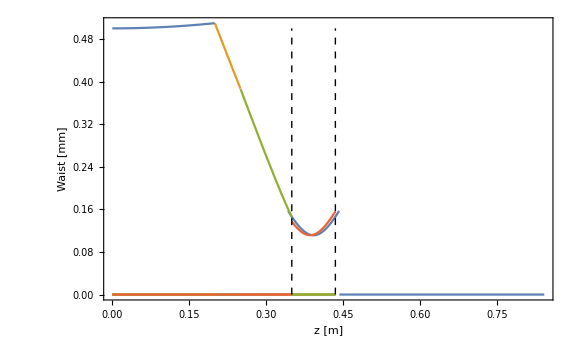

```mathematica
zR=(π wCav^2)/λ;
qStart =q0;
d0=.20; 
dCavity =d0+d1+d2+ LCav/2;
system={
{{{1,0},{0,1}},d0},
{MLens[f1],d1},
{MLens[f2],d2},
{MMirror1,LCav}
}/.soln[[1]];
Show[Plot[Piecewise[{{w[z-dCavity,wCav]/10^-3,dCavity-zR<z <dCavity+zR}}],{z,0,dCavity+zR+0.4},PlotRange->{0,1.1w0/10^-3}],beamPropagate[qStart,system],Graphics[{Dashed,Line[{{dCavity-LCav/2,0},{dCavity-LCav/2,w0/10^-3}}]}],
Graphics[{Dashed,Line[{{dCavity+LCav/2,0},{dCavity+LCav/2,w0/10^-3}}]}],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

Plot an approximate solution with lenses on hand

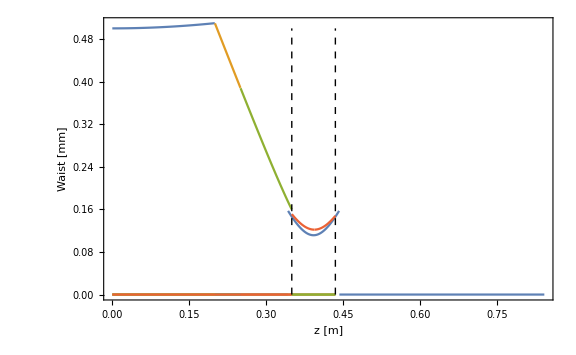

```mathematica
d0=.20; 
dCavity =d0+d1+d2+ LCav/2;
system={
{{{1,0},{0,1}},d0},
{MLens[f1],d1}/.f1-> .2,
{MLens[f2],d2}/.f2->∞,
{MMirror1,LCav}
}/.soln[[1]];
Show[Plot[Piecewise[{{w[z-dCavity,wCav]/10^-3,dCavity-zR<z <dCavity+zR}}],{z,0,dCavity+zR+0.4},PlotRange->{0,1.1w0/10^-3}],beamPropagate[qStart,system],Graphics[{Dashed,Line[{{dCavity-LCav/2,0},{dCavity-LCav/2,w0/10^-3}}]}],
Graphics[{Dashed,Line[{{dCavity+LCav/2,0},{dCavity+LCav/2,w0/10^-3}}]}],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

```mathematica
R = 0.005;
LCav = 2*R;
f=-R/2;
λ=7.8*^-7;
w0=5*-6; (*waist in μm*)
q0 = -ⅈ (π w0^2)/λ; (*initial beam parameter*)
wCav = w0;(*approx TEM00 waist to match in cavity*)
zR=(π wCav^2)/λ;
qStart =q0;
d0=R; 
d1=R/2;
dCavity =R;
system={
{{{1,0},{0,1}},d0},
{MLens[f],0.001},
{MLens[0.0035],d1}
};
Show[beamPropagate[qStart,system],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

-Graphics-

```mathematica
((7+1.6)/(7*1.6))^-1
```

1.30233